#### Q:How to calculate the Integrate ∫_0^∞ (x^2+1)/(x^4+1)ⅆx? 1.Get Singularities

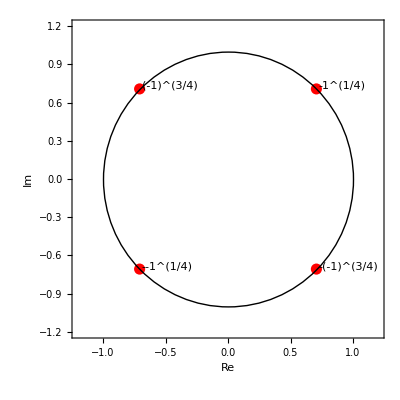

```mathematica
data=x/.#&/@Solve[x^4+1 == 0];

p=ListPlot[Labeled[{Re[#],Im[#]},#]&/@data,AxesOrigin->{0,0},PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]]];

Show[p,Graphics@Circle[{0,0},1]]
```

#### 2.Calculating residues

```mathematica
f[z_]:=(z^2+1)/(z^4+1);
int = 2Pi*I(Residue[f[z],{z,data[[2]]}]+Residue[f[z],{z,data[[4]]}])//Simplify;
int/2
```

π/(√2)